# 1. PRAKTIKA

```mathematica
Clear["Global`*"]
```

## TEORIA

### a)

```mathematica
2+6*3
```

20

```mathematica
6/3+3
```

5

```mathematica
2 2
```

4

si se deja espacio entre dos numeros, se multiplican.

Sqrt[]
Log[] //defektuz ln
Power[a, x]
Exp[]
Sin[]
Cos[]
Abs[]

```mathematica
Abs[(Sin[0.5]+Log[E^2])/ (Cos[1.2]-Sqrt[23])]
```

0.559251

```mathematica
N[(4/3),5]
```

1.3333

bigarren argumentua zenbat digitu esanguratzu agertzen diren da.

### Zerrendak

```mathematica
zerrenda = {1,2,3,4,5,6}
```

{1,2,3,4,5,6}

```mathematica
berredura=Table[2^i,{i,10}]
```

{2,4,8,16,32,64,128,256,512,1024}

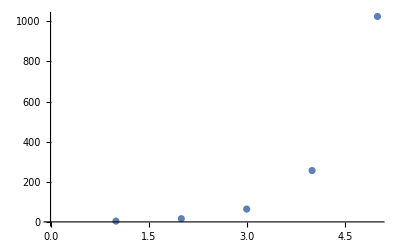

```mathematica
ListPlot[Table[2^i,{i,2,10,2}]]
```

```mathematica
berredura2=Table[8i,{i,50}]
```

{8,16,24,32,40,48,56,64,72,80,88,96,104,112,120,128,136,144,152,160,168,176,184,192,200,208,216,224,232,240,248,256,264,272,280,288,296,304,312,320,328,336,344,352,360,368,376,384,392,400}

```mathematica
zerrenda[[3]]
```

3

```mathematica
zerrenda[[4]]
```

4

```mathematica
berredura2[[4]]
```

32

### Matrizeak eta determinanteak

```mathematica
Clear["Global`*"]
```

```mathematica
a={{1,2,3},{0,1,5}};
```

```mathematica
MatrixForm[a]
```

(1 | 2 | 3
0 | 1 | 5)

```mathematica
Table[10*i+j,{i,1,3},{j,1,3}]
```

{{11,12,13},{21,22,23},{31,32,33}}

```mathematica
Flatten[a]
```

{1,2,3,0,1,5}

```mathematica
b=DiagonalMatrix[{2,1,4}]
```

{{2,0,0},{0,1,0},{0,0,4}}

```mathematica
Dimensions[b]
```

{3,3}

```mathematica
Transpose[a]
```

{{1,0},{2,1},{3,5}}

```mathematica
IdentityMatrix[3]
```

{{1,0,0},{0,1,0},{0,0,1}}

```mathematica
MatrixPower[b,3]
```

{{8,0,0},{0,1,0},{0,0,64}}

```mathematica
a^3
```

{{1,8,27},{0,1,125}}

```mathematica
Transpose[a][[1]]
```

{1,0}

```mathematica
c={{1,2,3},{0,1,5},{1,0,1}}
```

{{1,2,3},{0,1,5},{1,0,1}}

```mathematica
Det[c]
```

8

```mathematica
Inverse[c]
```

{{1/8,-1/4,7/8},{5/8,-1/4,-5/8},{-1/8,1/4,1/8}}

```mathematica
MatrixRank[c]
```

3

```mathematica
d={{3,3,3,m},{3,3,m,3},{3,m,3,3},{3,3,3,3}};
```

```mathematica
s=Solve[Det[d]==0,m]
```

{{m→3},{m→3},{m→3}}

```mathematica
Det[d]
```

-81+81 m-27 m^2+3 m^3

## ARIKETAK

### 1.Ariketa

### 2.Ariketa

### 3.Ariketa

```mathematica
c={{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}
```

{{4,1,3,1,3},{2,6,3,-1,2},{1,3,4,1,1},{-4,5,4,2,-3},{1,-1,-3,-1,2}}

```mathematica
MatrixForm[c]
```

(4 | 1 | 3 | 1 | 3
2 | 6 | 3 | -1 | 2
1 | 3 | 4 | 1 | 1
-4 | 5 | 4 | 2 | -3
1 | -1 | -3 | -1 | 2)

#### a)

```mathematica
Transpose[c]⟦3⟧
```

{3,3,4,4,-3}

#### b)

```mathematica
c1=c[[{2,3,4,5},{1,2,4,5}]]
```

{{2,6,-1,2},{1,3,1,1},{-4,5,2,-3},{1,-1,-1,2}}

```mathematica
MatrixForm[c1]
```

(2 | 6 | -1 | 2
1 | 3 | 1 | 1
-4 | 5 | 2 | -3
1 | -1 | -1 | 2)

```mathematica
Det[c1]
```

-63

#### c)

```mathematica
Inverse[c]
```

{{91/120,7/24,-4/3,5/24,-9/20},{41/120,5/24,-2/3,7/24,1/20},{-21/40,-1/8,1,-3/8,-3/20},{7/8,-1/8,-1,5/8,1/4},{-67/120,-7/24,4/3,-5/24,13/20}}

```mathematica
Inverse[c]//MatrixForm
```

(91/120 | 7/24 | -4/3 | 5/24 | -9/20
41/120 | 5/24 | -2/3 | 7/24 | 1/20
-21/40 | -1/8 | 1 | -3/8 | -3/20
7/8 | -1/8 | -1 | 5/8 | 1/4
-67/120 | -7/24 | 4/3 | -5/24 | 13/20)

### 4.Ariketa

#### a)

```mathematica
e={{1,1,1,1},{-m,1,1,2},{1,-m,1,3},{1,1,-m,4}};
```

```mathematica
MatrixForm[e]
```

(1 | 1 | 1 | 1
-m | 1 | 1 | 2
1 | -m | 1 | 3
1 | 1 | -m | 4)

#### b)

```mathematica
Solve[Det[e]== 0,m]
```

{{m→-7},{m→-1},{m→-1}}

m != -7 eta m != -1  denean, matrizearen heina 4 izango da .

```mathematica
MatrixRank[e/.m->-3]
```

4

m = -7 denean :

```mathematica
MatrixRank[e/.m->-7]
```

3

m = -1 denean:

```mathematica
MatrixRank[e/.m->-1]
```

2

#### c)

```mathematica
Inverse[e/.m->2]//MatrixForm
```

(1/3 | -8/27 | 1/27 | 1/27
1/3 | 2/27 | -7/27 | 2/27
1/3 | 1/9 | 1/9 | -2/9
0 | 1/9 | 1/9 | 1/9)

#### d)

```mathematica
MatrixPower[e/.m->-1,5]
```

{{778,778,778,2332},{1037,1037,1037,3110},{1296,1296,1296,3888},{1555,1555,1555,4666}}

```mathematica
MatrixPower[e/.m->-1,5]//MatrixForm
```

(778 | 778 | 778 | 2332
1037 | 1037 | 1037 | 3110
1296 | 1296 | 1296 | 3888
1555 | 1555 | 1555 | 4666)

### 5.Ariketa

```mathematica
d={{1,a,-1,1},{2,1,-a,2},{1,-1,-1,a-1}};
```

```mathematica
MatrixForm[d]
```

(1 | a | -1 | 1
2 | 1 | -a | 2
1 | -1 | -1 | -1+a)

#### a)

```mathematica
minoreak=Minors[d,3]
```

{{2+a-a^2,-2+5 a-2 a^2,-4+4 a-a^2,2 a+a^2-a^3}}

```mathematica
Solve[minoreak =={{0,0,0,0}},a]
```

{{a→2}}

```mathematica
MatrixRank[d/.a->2]
```

2

```mathematica
MatrixRank[d/.a->1]
```

3

#### b)

```mathematica
d1=d/.a->3;
```

```mathematica
d2=d1[[{2,3},{1,3}]]
```

{{2,-3},{1,-1}}

```mathematica
MatrixRank[d2]
```

2

#### c)

```mathematica
d3=d/.a->2
```

{{1,2,-1,1},{2,1,-2,2},{1,-1,-1,1}}

```mathematica
Minors[d3,2]
```

{{-3,0,0,-3,3,0},{-3,0,0,-3,3,0},{-3,0,0,-3,3,0}}

```mathematica
Minors[d3,2]//MatrixForm
```

(-3 | 0 | 0 | -3 | 3 | 0
-3 | 0 | 0 | -3 | 3 | 0
-3 | 0 | 0 | -3 | 3 | 0)